#### p(x) AG (1,10) inverted by AG (1,10): Frictionless punch_Geom 10x10, 40x40 mesh, compute nodal traction and interpolated P(x)

Import::nffil: File C:\Users\nguye\OneDrive - UCB-O365\Haden\Los Alamos NL\Work\2025_10_19_FEM static_larger dimension, bonded and frictionless\Frictionless_punch_10x10geom\force_control(40,40)_rigid_punch_(1,10,1,10,10)_dz=-0.1\nodal_displacement_disp_control_(1,10).xlsx not found during Import.

Set::shape: Lists {data} and $Failed are not the same shape.

{4.,4.125,4.25,4.375,4.5,4.625,4.75,4.875,5.,5.125,5.25,5.375,5.5,5.625,5.75,5.875,6.}

{-3.09703×10^6,-1.33988×10^7,727507.,-4.26852×10^6,-1.96355×10^6,-3.70879×10^6,-1.77165×10^6,-3.48292×10^6,-1.72073×10^6,-3.48292×10^6,-1.77165×10^6,-3.70879×10^6,-1.96355×10^6,-4.26852×10^6,727507.,-1.33988×10^7,-3.09703×10^6}

{{1,10,1,10,2},{1,1,1,1,1},{1,1,1,1,1},{1,1,1,1,1},{1,1,1,1,1},{1,1,1,1,1},{1,1,1,1,1},{1,10,1,10,1}}

Nodal traction vectors P(1,10) = {-4.671×10^8,-3.785×10^7,-3.166×10^7,-2.502×10^7,-2.432×10^7,-2.209×10^7,-2.148×10^7,-2.084×10^7,-2.076×10^7,-2.084×10^7,-2.148×10^7,-2.209×10^7,-2.432×10^7,-2.502×10^7,-3.166×10^7,-3.785×10^7,-4.671×10^8}

p(x) resultant force P(1,10) = -6.36482×10^7

C:\Users\nguye\OneDrive - UCB-O365\Haden\Los Alamos NL\Work\2025_10_19_FEM static_larger dimension, bonded and frictionless\Frictionless_punch_10x10geom\force_control(40,40)_rigid_punch_(1,10,1,10,10)_dz=-0.1\NodalTraction.xlsx

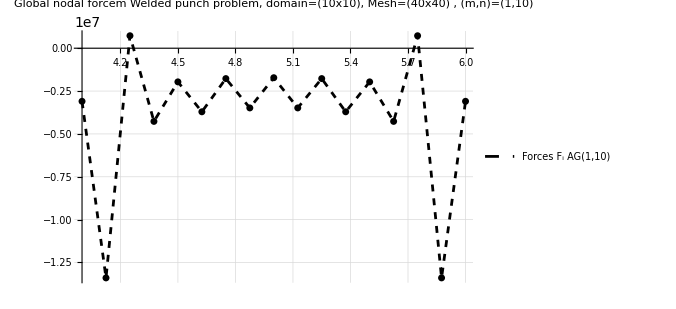

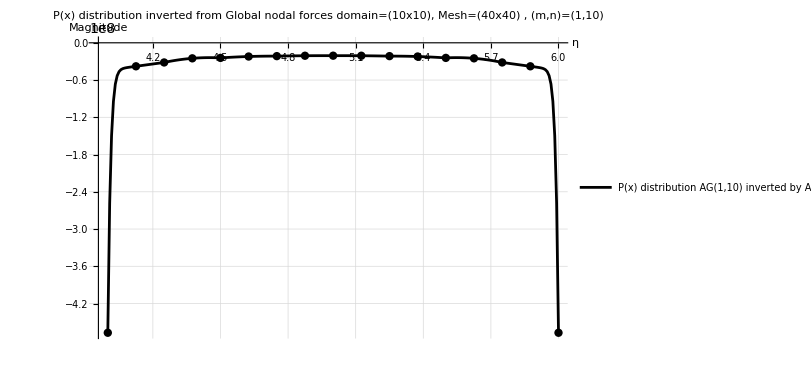

```mathematica
(*Get the nodal force from Python*)
dir="C:\\Users\\nguye\\OneDrive - UCB-O365\\Haden\\Los Alamos NL\\Work\\2025_10_19_FEM static_larger dimension, bonded and frictionless\\Frictionless_punch_10x10geom\\force_control(40,40)_rigid_punch_(1,10,1,10,10)_dz=-0.1";
filename="nodal_displacement_disp_control_(1,10).xlsx";
{data}=Import[FileNameJoin[{dir,filename}]];
raw=Rest[data];
underpunchdata=raw[[6513;;6529]];
xcoordglobal=underpunchdata[[All,2]]
underpunchdata//MatrixForm;
Fy=underpunchdata[[All,7]](*Nodal Reaction force/*)
Clear[x]
nx=40;
ny=40;
gx=10; gy=10;
nele=8; (*For*)
{m1,n1,m2,n2}={1,10,1,10};
AGtype=Table[{1,1,1,1,1},{i,1,nele}];
AGtype[[1]]={m1,n1,m2,n2, 2};
AGtype[[-1]]={m1,n1,m2,n2, 1};
AGtype

q2LineConnectivity[ne_Integer]:=Partition[Range[2 ne+1],3,2]
conns=q2LineConnectivity[nele];
(****************)
(*Input*)
xcoord=Partition[xcoordglobal,3,2];(*element nodal x-coordinate*)

Mmat=GlobalMmat[xcoord,conns,AGtype]; (*Global M matrix*)
Pvec=LinearSolve[Mmat,Fy]; (* Compute Nodal traction vector *)

Pxdata=PxinterpolatedData[Pvec,AGtype,xcoord];
Pvecdata=Transpose[{xcoordglobal,Pvec}];
totalResutant=ComputeResultant[Pelem,xcoord,AGtype];
Print[Style[Row[{"Nodal traction vectors P(",m,",",n,") = ", NumberForm[Pvec,{Infinity,3}]}],16, Bold,Blue]];
Print[Style[Row[{"p(x) resultant force P(",m,",",n,") = ", totalResutant}],16,Bold,Red]];
Export[FileNameJoin[{dir,"NodalTraction.xlsx"}],Pvec]

Clear[x]
Color=Black;
label="P(x) distribution AG(1,10) inverted by AG(1,10)";

Fydata=Transpose[{xcoordglobal,Fy}];
FvecPlotAG=ListLinePlot[Fydata,PlotStyle->{Color,Dashed},PlotRange->{{4,6},All},PlotLegends->Placed[{"Forces F_i AG(1,10)"},{0.7,0.3}],PlotLabel->Style[Row[{"Global nodal forcem Welded punch problem, \n domain=(",gx,"x",gy,"), Mesh=(", 40,"x",ny,") , (m,n)=(",m1,",",n1,")"}],Bold,16], GridLines->Automatic,ImageSize->500,TicksStyle->Directive["Label",Bold, 12]];
FvecDotAG=ListPlot[Fydata,PlotStyle->{Color,PointSize[0.01]}];

Clear[x]
pxexact=(-19.9*10^6)/(√(1-(x-5)^2)); (*P(x) distribution is centered at x=5, singular at x=4 & 6*)

PxexactPlot=Plot[pxexact,{x,4,6},PlotStyle->{Black,Dashed},PlotRange->All,PlotLegends->Placed[{"P(x) exact"},{0.7,0.3}],PlotLabel->Style[" Exact solution",16], GridLines->Automatic,ImageSize->600];
(**********************)
PxplotAG110110=ListLinePlot[Pxdata,PlotRange->{All,All},PlotStyle->{Color},PlotLegends->Placed[{label},{0.7,0.3}],AxesLabel->{Style["η",Bold,16],Style["Magnitude",Bold,16]},PlotLabel->Style[Row[{" P(x) distribution inverted from Global nodal forces \n domain=(",gx,"x",gy,"), Mesh=(",40,"x",ny,") , (m,n)=(",m1,",",n1,")"}],Bold,16], 
TicksStyle->{16,Bold}, TicksStyle->Directive["Label",Bold, 12],
GridLines->Automatic,ImageSize->600];

PvecPlotAG=ListPlot[Pvecdata,PlotStyle->{Color,PointSize[0.01]}(*,PlotLegends->Placed[{"Nodal traction P_i"},{0.8,0.3}]*)];

Fy110=Show[FvecPlotAG,FvecDotAG]
plot110110=Show[PxplotAG110110,PvecPlotAG]
```

```mathematica
-6.3648218307325944*^7
```

C:\Users\nguye\OneDrive - UCB-O365\Haden\Los Alamos NL\Work\2025_10_19_FEM static_larger dimension, bonded and frictionless\Welded_punch_10x10geom\disp_control(40,40)_rigid_punch_(1,10,1,10,10)_dz=-0.1\NodalTraction.xlsx

-Graphics-

-Graphics-